## Plot kappa Barbosa curves for Chris

#### The cylindrical-coord version of the Barbosa func, in terms of bulk velocity v_(b,th) = v_b/v_th=√(ΔΦ/(k T)) normalized by the thermal velocity v_th= √(kT/m)(origin: journal__20180125__somesing_work)

```mathematica
vbth[deltaPhi_,T_]:=√(deltaPhi/T);
```

```mathematica
normFacAlt[vbth_,kappa_]:=2/(π^(1/2)(kappa - 3/2)^(3/2))(1/2 Gamma[kappa-1/2]/Gamma[kappa+1]+vbth/(√π kappa(kappa-3/2)^(1/2))Hypergeometric2F1[1/2,kappa,3/2,-vbth^2/(kappa-3/2)])^-1;
funcAlt[rho_,phi_,vbth_,kappa_,b_]:=(1+(rho^2+vbth^2-2 vbth rho (1 - (Sin[phi])^2 b)^(1/2))/(kappa-3/2 ))^(-(kappa+1))
```

### The original Barbosa [1977] relation, for reference

```mathematica
barbDist[vpar_,vperp_,deltaPhi_,T_,alpha_]:=4/(π^(1/2)Erfc[-√(deltaPhi/T)])Exp[-1(vpar^2+vperp^2+deltaPhi/T-2 √(deltaPhi/T) (vpar^2+ vperp^2 (1 - alpha) )^(1/2))] UnitStep[vpar]
barbAsymp[deltaPhi_,T_]:=1+2(√(deltaPhi/T))/Erfc[-√(deltaPhi/T)] NIntegrate[Erfc[x],{x,-√(deltaPhi/T),∞}]
```

```mathematica
dPhi=941;Tm=110;
vb[kappa_]:=√(dPhi/(Tm(1-3/(2 kappa))))
vbAlt=√(dPhi/Tm);
```

#### Some plot options

```mathematica
colors={Black,Gray,Orange,Red,Brown,Green,Purple};
kappas = {1.55,1.6,1.8,2,2.45,4};
```

```mathematica
placeList={Above,Above,Above,Above,Above,Above,Above};
nDigs={3,2,2,2,3,1,2,2};
kapStrVals=Table[NumberForm[kappas[[k]],nDigs[[k]]],{k,1,6}];
kappaLabels=Table[StringForm["κ = `1`",kapStrVals[[k]]],{k,1,6}];
nDigitsdPhi=3;nDigitsTm=3;
RBMin=1;RBMax=10000;
```

```mathematica
showers={1,2,3,4,5,6};
(*showers={1};*)
```

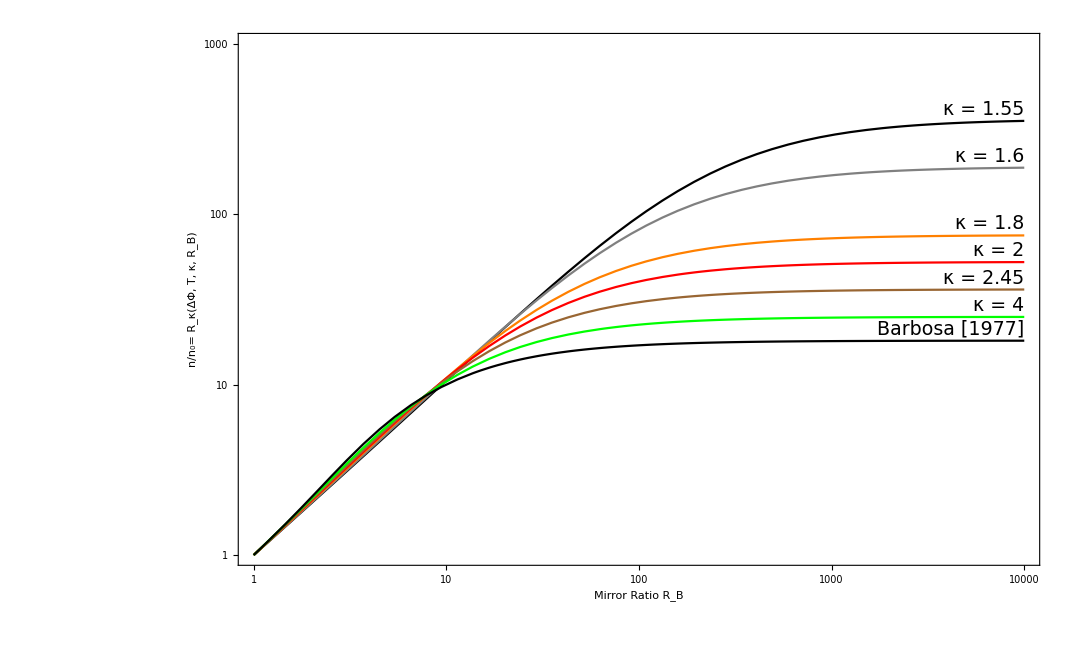

```mathematica
Show[Table[LogLogPlot[NIntegrate[rho^2 Sin[phi]  normFacAlt[vbth[dPhi,Tm],kappas[[k]]]funcAlt[rho,phi,vbth[dPhi,Tm],kappas[[k]],1/RB],{rho,0,∞},{phi,0,π/2}],{RB,RBMin,RBMax},PlotRange->{{RBMin,RBMax},{1,1000}},PlotStyle->colors[[k]],Frame->True,PlotLabels ->Placed[kappaLabels[[k]] ,placeList[[k]]],LabelStyle->(FontSize->19),FrameLabel->{{StringForm["n/n_0= R_κ(ΔΦ, T, κ, R_B)"],""},{StringForm["Mirror Ratio R_B"],StringForm["ΔΦ = `1`; T_m= `2` eV; ϕ̄= `3`",NumberForm[dPhi,nDigitsdPhi],NumberForm[Tm,nDigitsTm],NumberForm[N[dPhi/Tm],{3,1}]]}},ImageSize->900],{k,showers}],LogLogPlot[NIntegrate[vperp barbDist[vpar,vperp,dPhi,Tm,1/RB],{vpar,0,∞},{vperp,0,∞}],{RB,RBMin,RBMax},PlotRange->{{RBMin,RBMax},{1,1000}},PlotStyle->Black,Frame->True,FrameStyle->Black,PlotLabels ->Placed[StringForm["Barbosa [1977]"] ,Above],LabelStyle->(FontSize->19),FrameLabel->{{StringForm["n/n_0= R_κ(ΔΦ, T, κ, R_B)"],""},{StringForm["Mirror Ratio R_B"],StringForm["ΔΦ = `1`; T_m= `2` eV; ϕ̄= `3`",NumberForm[dPhi,nDigitsdPhi],NumberForm[Tm,nDigitsTm],NumberForm[N[dPhi/Tm],{3,1}]]}},ImageSize->900]]
```

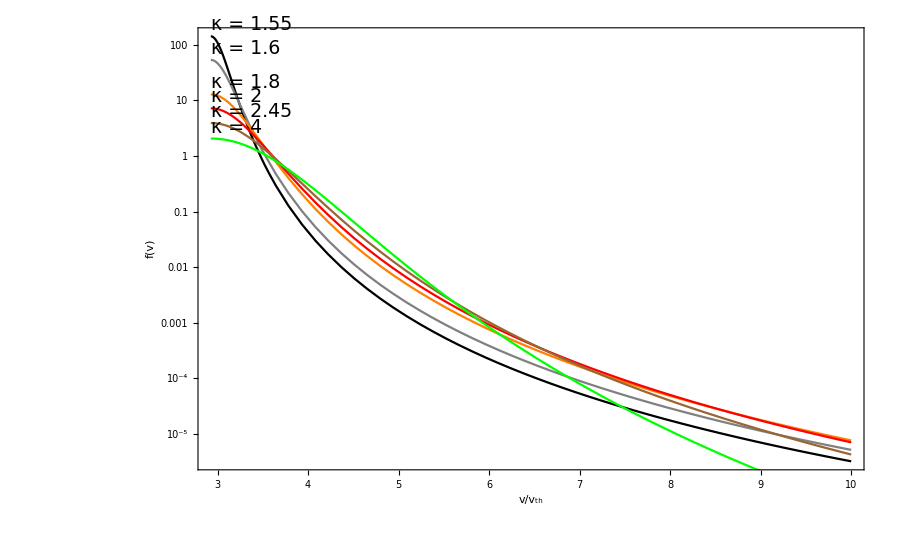

```mathematica
Show[Table[LogPlot[normFacAlt[vbth[dPhi,Tm],kappas[[k]]]funcAlt[rho,0,vbth[dPhi,Tm],kappas[[k]],0],{rho,vbth[dPhi,Tm],10},PlotStyle->colors[[k]],Frame->True,PlotLabels ->Placed[kappaLabels[[k]] ,placeList[[k]]],LabelStyle->(FontSize->19),FrameLabel->{StringForm["v/v_th"],StringForm["f(v)"]},ImageSize->900],{k,showers}]]
```

```mathematica
b=1/10000;
```

```mathematica
this={Table[{kaps,NIntegrate[rho^2 Sin[phi]  normFacAlt[vbth[dPhi,Tm],kaps]funcAlt[rho,phi,vbth[dPhi,Tm],kaps,b],{rho,0,∞},{phi,0,π/2}]},{kaps,kappas}],{∞,NIntegrate[vperp barbDist[vpar,vperp,dPhi,Tm,b],{vpar,0,∞},{vperp,0,∞}]}}
```

{{{1.55,352.415},{1.6,187.285},{1.8,75.0172},{2,52.3215},{2.45,36.1318},{4,24.9476}},{∞,18.0979}}

#### Here are the asymptotic values given by the kappa Barbosa and the Barbosa [1977] relation

```mathematica
b=0;
```

```mathematica
asymp=Table[{kaps,NIntegrate[rho^2 Sin[phi]  normFacAlt[vbth[dPhi,Tm],kaps]funcAlt[rho,phi,vbth[dPhi,Tm],kaps,b],{rho,0,∞},{phi,0,π/2}]},{kaps,kappas}];
```

```mathematica
asymp=Append[asymp,{∞,NIntegrate[vperp barbDist[vpar,vperp,dPhi,Tm,b],{vpar,0,∞},{vperp,0,∞}]}]
```

{{1.55,360.688},{1.6,189.538},{1.8,75.3484},{2,52.4731},{2.45,36.1975},{4,24.9745},{∞,18.1094}}

```mathematica
NumberForm[asymp[[All,2]]/Last[asymp[[All,2]]],{3,3}]
```

{19.900,10.500,4.160,2.900,2.000,1.380,1.000}

#### Here are the values of the peaks of each function

```mathematica
b=1;
```

```mathematica
peaks=N[Table[{kaps,normFacAlt[vbth[dPhi,Tm],kaps]funcAlt[vbth[dPhi,Tm],0,vbth[dPhi,Tm],kaps,b]},{kaps,kappas}]];
```

```mathematica
peaks=Append[peaks,N[{∞,barbDist[vbth[dPhi,Tm],0,dPhi,Tm,b]}]]
```

{{1.55,142.992},{1.6,53.7172},{1.8,12.8638},{2.,7.22276},{2.45,3.92152},{4.,2.06331},{∞,1.1284}}

```mathematica
NumberForm[peaks[[All,2]]/Last[peaks[[All,2]]],{3,3}]
```

{127.000,47.600,11.400,6.400,3.480,1.830,1.000}